```mathematica
(*P50 HW1*)
(*Each question is worth 1 pt. You can type your answer directly below the questions. Please upload your solution in .nb or .pdf*)
```

```mathematica
(*Q1: Please use RandomPrime[] function to give a (pseudo)random prime number between 200 and 300.*)
```

```mathematica
RandomPrime[{200,300}]
```

211

```mathematica
(*Q2:What is the 400th prime number?
Is 24781 a prime number?*)
```

```mathematica
Prime[400]
```

2741

```mathematica
PrimeQ[24781]
```

True

```mathematica
(*Q3: Plot the 2th, 4th, 6th,... 20th prime numbers)
```

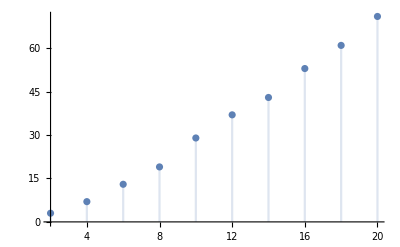

```mathematica
DiscretePlot[Prime[x],{x,{2, 4,6, 8, 10, 12,14,16,18,20}}]
```

```mathematica
(*Q4: Solve the following set of equtions
vb 0.5 + vr 0.5 == 12
vr 1/4 + vb 3/4 == 16
*)
```

```mathematica
Solve[{vb 0.5 + vr 0.5 == 12, vr 1/4 + vb 3/4 == 16},{vb, vr}]
```

{{vb→20.,vr→4.}}

```mathematica
(*Q5: Let function f(x) = x/(Sqrt[x^2-a^2]). calculate and simplify the 1st, 2nd and 3rd order derivatives of f(x)*)
```

```mathematica
f[x_]:= x/(Sqrt[x^2-a^2])
D[f[x],x]//FullSimplify
D[f[x],{x,2}]//FullSimplify
D[f[x],{x,3}]//FullSimplify
```

-a^2/((-a^2+x^2)^(3/2))

(3 a^2 x)/((-a^2+x^2)^(5/2))

-(3 (a^4+4 a^2 x^2))/((-a^2+x^2)^(7/2))

```mathematica
(*Q6: Perform integral of f(x) = x^2/(a^2-x^2)*)
```

```mathematica
Integrate[x^2/(a^2-x^2),x]
```

-x+a ArcTanh[x/a]

```mathematica
(*Q7: Perform integral of f(x) = E^(- k x)Sin[x] from x=0 to x= infinity, where the real part of k is positive.*)
```

```mathematica
Assuming[Re[k]>0,Integrate[E^(-k x)Sin[x],{x,0,Infinity}]]
```

1/(1+k^2)

```mathematica
(*Q8: Solve the numerial solution of the following set of equations: 
   y == -2 x^2 + 10 x + 5
y == 2 x -1}
     Then plot  y == -2 x^2 + 10 x + 5 and y == 2 x -1 in the same plot, and check the intersects of the two curves using your cursor.
*)
```

{y==5+10 x-2 x^2,y==-1+2 x}

{{x→2-√7,y→3-2 √7},{x→2+√7,y→3+2 √7}}

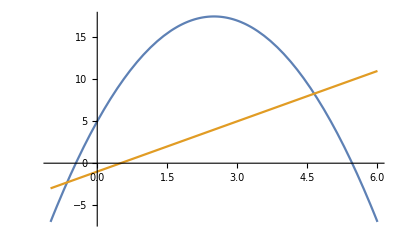

```mathematica
{y == -2 x^2 + 10 x + 5,y == 2 x -1}
Solve[%]
Plot[{-2 x^2 + 10 x + 5,2 x -1},{x,-1,6}]
```

```mathematica
(*Q9: Find the determinant of ({{3, 2, 4, 5}, {2, 0, 2, -1}, {4, 2, 3, 0}, {-2, 7, 1, 9}}) .
A = ({{49, 38, -69}, {-34, -123, 40}, {-38, 173, 74}}), B = ({{6, -4, 0}, {-2, 13, 8}, {5, 7, -1}}), find the commutator A.B - B.A.*)
```

```mathematica
Det[({{3, 2, 4, 5}, {2, 0, 2, -1}, {4, 2, 3, 0}, {-2, 7, 1, 9}})]
```

-109

```mathematica
A = ({{49, 38, -69}, {-34, -123, 40}, {-38, 173, 74}})
B = ({{6, -4, 0}, {-2, 13, 8}, {5, 7, -1}})
A.B - B.A//MatrixForm
```

{{49,38,-69},{-34,-123,40},{-38,173,74}}

{{6,-4,0},{-2,13,8},{5,7,-1}}

(-557 | -905 | 947
1086 | -892 | -2274
-249 | 3763 | 1449)

```mathematica
(*Q10: Solve (and simplify) the differential equation x''[t]+2x'[t]+x[t]== Cos[ω t] with the conditions x[0]==0 and x'[0]==0. *)
```

```mathematica
DSolve[{x''[t]+2x'[t]+x[t]== Cos[ω t], x[0]==0,x'[0]==0},x[t],t]//FullSimplify
```

{{x[t]→(ⅇ^-t (-1+ω^2-t (1+ω^2)+ⅇ^t (-(-1+ω^2) Cos[t ω]+2 ω Sin[t ω])))/((1+ω^2)^2)}}